```mathematica
Range@5
```

{1,2,3,4,5}

```mathematica
Subsets[Out[1]]
```

{{},{1},{2},{3},{4},{5},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5},{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5},{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5},{1,2,3,4,5}}

```mathematica
Intersection[{},Range@5]
```

{}

```mathematica
Union[{},Range@5]
```

{1,2,3,4,5}

```mathematica
{{},{1},{2,3,4,5},Range@5}
```

{{},{1},{2,3,4,5},{1,2,3,4,5}}

```mathematica
Subsets[Range@3]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Range@7
```

{1,2,3,4,5,6,7}

```mathematica
Range[0,6]
```

{0,1,2,3,4,5,6}

```mathematica
FullSimplify[ArcCurvature[{Cos[t],Sin[t]},t],t∈Reals]
```

1

```mathematica
FullSimplify[D[{Cos[t],Sin[t]},t].D[{Cos[t],Sin[t]},{t,2}],t∈Reals]
```

0

```mathematica
x^2
```

x^2

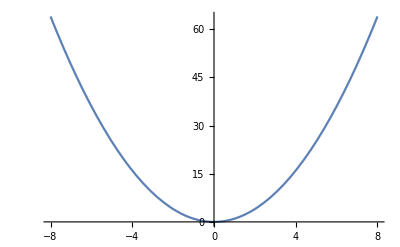

```mathematica
Plot[x^2,{x,-8,8}]
```

```mathematica
FullSimplify[ArcLength[{x,x^2},x]]
```

ArcLength::vars: Integration range specification x is not of the form {t, t_min, t_max}.

ArcLength[{x,x^2},x]

```mathematica
FullSimplify[ArcLength[{x,x^2},{x,0,a}]]
```

1/4 (2 a √(1+4 a^2)+ArcSinh[2 a])

```mathematica
FullSimplify[ArcLength[{x,x^2},{x,0,a}],a∈Reals]
```

1/4 (2 a √(1+4 a^2)+ArcSinh[2 a])

```mathematica
Integrate[√(1+f'[x]^2),{x,0,a}]
```

∫_0^a √(1+f'[x]^2)ⅆx

```mathematica
Integrate[f[x],{x,0,a}]==1/4(2a f[x]+ArcSinh[2 a])
```

∫_0^a f[x]ⅆx==1/4 (ArcSinh[2 a]+2 a f[x])

```mathematica
Reduce[∫_0^a f[x]ⅆx==1/4 (ArcSinh[2 a]+2 a f[x])]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[∫_0^a f[x]ⅆx==1/4 (ArcSinh[2 a]+2 a f[x])]

```mathematica
ArcCurvature[{x,f[x]},x]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
f''[x]/(√((1+f'[x]^2)^3))
```

f''[x]/(√((1+f'[x]^2)^3))

```mathematica
f[x+α]==f[x]+Integrate[f'[x],{x,0,α}]
```

f[x+α]==f[x]+∫_0^α f'[x]ⅆx

```mathematica
f[α+β]==f[α]+Integrate[f'[x],{x,α,β}]
```

f[α+β]==f[α]+∫_α^β f'[x]ⅆx

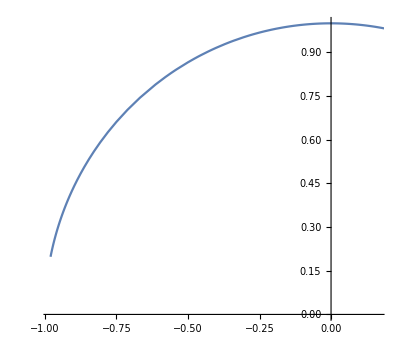

```mathematica
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,0,10}]
```

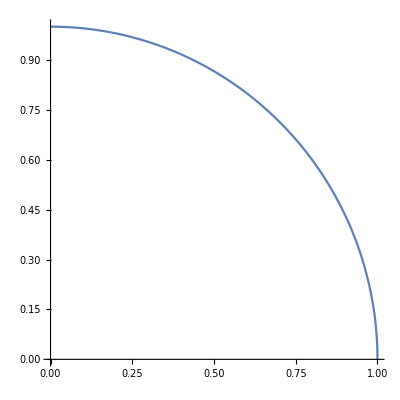

```mathematica
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,0,1}]
```

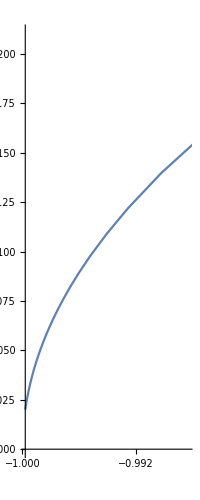

```mathematica
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,0,100}]
```

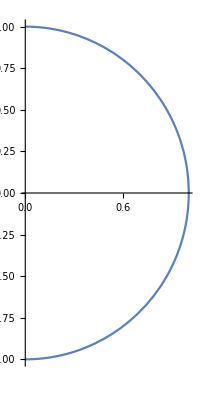

```mathematica
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,-1,1}]
```

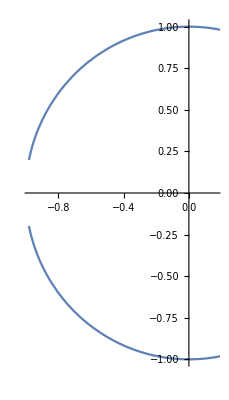

```mathematica
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,-10,10}]
```

```mathematica
Manipulate[
ParametricPlot[{(1-h^2)/(1+h^2),(2h)/(1+h^2)},{h,-a,a}]
,{a,1,100,10}]
```

```mathematica
units/t
```

units/t

```mathematica
units/t^2
```

units/t^2

```mathematica
(units/t^2)/((√(1+(units/t)^2))^3)
```

units/(t^2 (1+units^2/t^2)^(3/2))

```mathematica
ExpandAll[units/(t^2 (1+units^2/t^2)^(3/2))]
```

units/(t^2 √(1+units^2/t^2)+units^2 √(1+units^2/t^2))

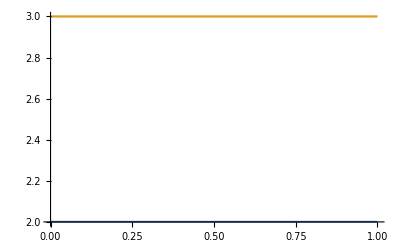

```mathematica
Plot[{2,3},{x,0,1}]
```

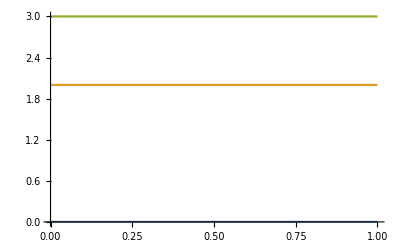

```mathematica
Plot[{0,2,3},{x,0,1}]
```

```mathematica
D[f[x+a],x]
```

f'[a+x]

```mathematica
Quantity[52,"Minutes"]+Quantity[8,"Seconds"]
```

3128 s

```mathematica
Quantity[3128, "Seconds"]/2.5
```

1251.2 s

```mathematica
UnitConvert[Quantity[1251.2,"Seconds"],MixedUnit[{"Minutes","Seconds"}]]
```

20 51.2

```mathematica
ArcSinh[x]
```

ArcSinh[x]

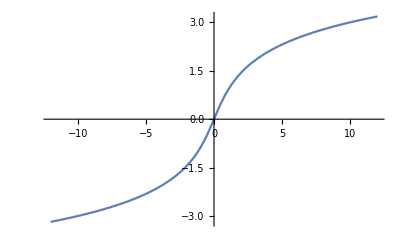

```mathematica
Plot[ArcSinh[x],{x,-12.,12.}]
```

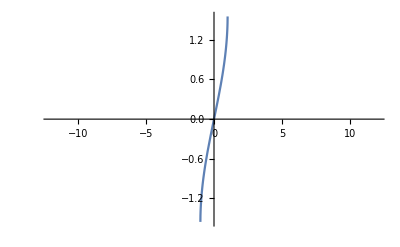

```mathematica
Plot[ArcSin[x],{x,-12.,12.}]
```

```mathematica
a x==x^2
```

a x==x^2

```mathematica
Solve[a x==x^2,x]
```

{{x→0},{x→a}}

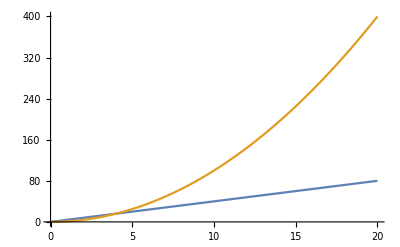

```mathematica
Plot[{4x,x^2},{x,0,20}]
```

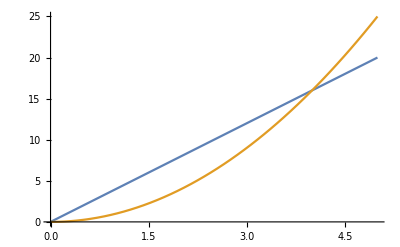

```mathematica
Plot[{4x,x^2},{x,0,5}]
```

```mathematica
Solve[4 x==x^2,x]
```

{{x→0},{x→4}}

```mathematica
Solve[(x-α)^2+β==x^2,x]
```

{{x→(α^2+β)/(2 α)}}

```mathematica
Solve[(x-α)^2+α^2==x^2,x]
```

{{x→α}}

```mathematica
f[x-α]+f[α]==f[x]
```

f[x-α]+f[α]==f[x]

```mathematica
With[{f=#^3&},
f[x-α]+f[α]==f[x]
]
```

(x-α)^3+α^3==x^3

```mathematica
With[{f=#^3&},
Solve[f[x-α]+f[α]==f[x],x]
]
```

{{x→0},{x→α}}

```mathematica
With[{f=#^3-#&},
Solve[f[x-α]+f[α]==f[x],x]
]
```

{{x→0},{x→α}}

```mathematica
Normalize[{x,a}].Normalize[{x,x^3}]
```

x^2/(√(Abs[a]^2+Abs[x]^2) √(Abs[x]^2+Abs[x]^6))+(a x^3)/(√(Abs[a]^2+Abs[x]^2) √(Abs[x]^2+Abs[x]^6))

```mathematica
FullSimplify[Normalize[{x,a}].Normalize[{x,x^3}],{x,a}∈Reals]
```

(x^2 (1+a x))/(√((a^2+x^2) (x^2+x^6)))

```mathematica
Manipulate[
((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))
,{a,-2,2}]
```

```mathematica
FullSimplify[Normalize[{x,a}].Normalize[{x,x^3-x}],{x,a}∈Reals]
```

((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))

```mathematica
Manipulate[
Plot[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4))),{x,-5,5}]
,{a,-2,2}]
```

```mathematica
Manipulate[
Plot[{x^3-x,a,((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))},{x,-5,5}]
,{a,-2,2}]
```

```mathematica
Manipulate[
Plot[{x^3-x,a,((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))},{x,-5,5},PlotRange->{-5,5}]
,{a,-2,2}]
```

```mathematica
FullSimplify[Abs[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))],{x,a}∈Reals]
```

Abs[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))]

```mathematica
Manipulate[
Plot[{x^3-x,a,Abs[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))]},{x,-5,5},PlotRange->{-5,5}]
,{a,-2,2}]
```

```mathematica
Abs[((x+a (-1+x^2)) Sign[x])/(√((a^2+x^2) (2-2 x^2+x^4)))]/.a->0
```

Abs[(x Sign[x])/(√(x^2 (2-2 x^2+x^4)))]

```mathematica
FullSimplify[Abs[(x Sign[x])/(√(x^2 (2-2 x^2+x^4)))],x∈Reals]
```

1/(√(2-2 x^2+x^4))

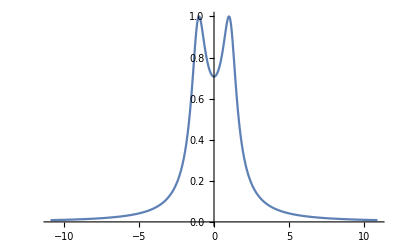

```mathematica
Plot[1/(√(2-2 x^2+x^4)),{x,-10.92,10.92}]
```

```mathematica
D[1/(√(2-2 x^2+x^4)),x]
```

-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))

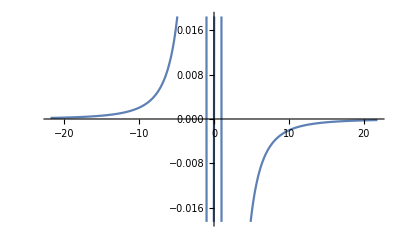

```mathematica
Plot[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2)),{x,-21.84,21.84}]
```

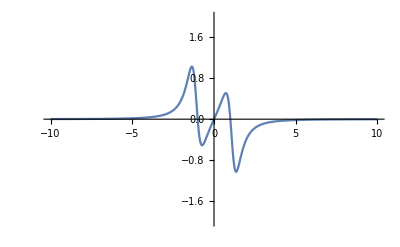

```mathematica
Plot[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2)),{x,-10,10},PlotRange->{-2,2}]
```

```mathematica
D[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2)),x]
```

(3 (-4 x+4 x^3)^2)/(4 (2-2 x^2+x^4)^(5/2))-(-4+12 x^2)/(2 (2-2 x^2+x^4)^(3/2))

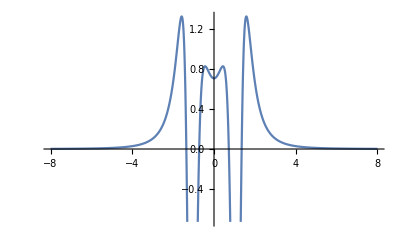

```mathematica
Plot[(3 (-4 x+4 x^3)^2)/(4 (2-2 x^2+x^4)^(5/2))-(-4+12 x^2)/(2 (2-2 x^2+x^4)^(3/2)),{x,-8,8}]
```

```mathematica
FindMaximum[1/(√(2-2 x^2+x^4)),{x,0}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{0.707107,{x→0.}}

```mathematica
FindMaximum[1/(√(2-2 x^2+x^4)),{x,1}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.,{x→1.}}

```mathematica
FindMaximum[1/(√(2-2 x^2+x^4)),x]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{1.,{x→1.}}

```mathematica
1/(√(2-2 x^2+x^4))/.x->1
```

1

```mathematica
LaplaceTransform[1/(√(2-2 x^2+x^4)),x,s]
```

LaplaceTransform[1/(√(2-2 x^2+x^4)),x,s]

```mathematica
Simplify[LaplaceTransform[1/(√(2-2 x^2+x^4)),x,s]]
```

LaplaceTransform[1/(√(2-2 x^2+x^4)),x,s]

```mathematica
FourierTransform[1/(√(2-2 x^2+x^4)),x,θ]
```

FourierTransform[1/(√(2-2 x^2+x^4)),x,θ]

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x]==1/(√(2-2 x^2+x^4)),{x,f[x]}∈Reals]
```

√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3))==1

```mathematica
DSolve[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3))==1,{f[x],f[x]},{x}]
```

$Aborted

```mathematica
DSolve[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3))==1,{f[x]},{x}]
```

$Aborted

```mathematica
LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3))==1,x,s]
```

LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3)),x,s]==1/s

```mathematica
NDSolve[LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3)),x,s]==1/s,{f[x],f[x]},{s,x,1+x}]
```

NDSolve::ndode: The equations {LaplaceTransform[√(((2-2 Power[«2»]+x^4) f''[x]^2)/(1+Power[«2»])^3),x,s]==1/s} are not differential equations or initial conditions in the dependent variables {TemporaryVariable$87368}.

NDSolve[LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3)),x,s]==1/s,{f[x],f[x]},{s,x,1+x}]

```mathematica
DSolve[LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3)),x,s]==1/s,{f[x],f[x]},{s}]
```

DSolve::deqx: Supplied equations are not differential or integral equations of the given functions.

DSolve[LaplaceTransform[√(((2-2 x^2+x^4) f''[x]^2)/((1+f'[x]^2)^3)),x,s]==1/s,{f[x],f[x]},{s}]